```mathematica
avgs= {{14.95,14.33,12.34,8.77,8.15,10.84,9.02,7.79,6.67,9.63,9.29,8.24,9.84,14.28,14.92,13.16},{14.54,15.62,12.73,11.51,11.79,11.47,11.43,9.02,8.57,11.15,10.64,10.3,12.09,14.49,14.88,14.71},{18.25,16.62,14.15,11.97,13.11,12.64,10.66,9.15,9.58,11.95,11.22,11.52,11.11,12.59,14.44,13.35},{16.02,16.81,15,11.53,10.18,12.2,11.78,8.36,8.15,10.36,10.74,8.25,9.99,12.42,11.39,11.06}}

stddev = {{0.51,0.27,0.27,0.33,0.31,0.38,0.26,0.37,0.27,0.29,0.26,0.27,0.25,0.33,0.3,0.25},{0.34,0.31,0.23,0.27,0.26,0.27,0.29,0.35,0.23,0.23,0.22,0.24,0.22,0.26,0.31,0.36},{0.45,0.31,0.24,0.34,0.3,0.22,0.23,0.24,0.28,0.28,0.24,0.36,0.23,0.25,0.31,0.28},{0.28,0.36,0.25,0.28,0.29,0.25,0.29,0.31,0.33,0.32,0.31,0.36,0.35,0.38,0.4,0.34}}
```

{{14.95,14.33,12.34,8.77,8.15,10.84,9.02,7.79,6.67,9.63,9.29,8.24,9.84,14.28,14.92,13.16},{14.54,15.62,12.73,11.51,11.79,11.47,11.43,9.02,8.57,11.15,10.64,10.3,12.09,14.49,14.88,14.71},{18.25,16.62,14.15,11.97,13.11,12.64,10.66,9.15,9.58,11.95,11.22,11.52,11.11,12.59,14.44,13.35},{16.02,16.81,15,11.53,10.18,12.2,11.78,8.36,8.15,10.36,10.74,8.25,9.99,12.42,11.39,11.06}}

{{0.51,0.27,0.27,0.33,0.31,0.38,0.26,0.37,0.27,0.29,0.26,0.27,0.25,0.33,0.3,0.25},{0.34,0.31,0.23,0.27,0.26,0.27,0.29,0.35,0.23,0.23,0.22,0.24,0.22,0.26,0.31,0.36},{0.45,0.31,0.24,0.34,0.3,0.22,0.23,0.24,0.28,0.28,0.24,0.36,0.23,0.25,0.31,0.28},{0.28,0.36,0.25,0.28,0.29,0.25,0.29,0.31,0.33,0.32,0.31,0.36,0.35,0.38,0.4,0.34}}

```mathematica
ListPlot3D[avgs,PlotTheme->"Scientific",ColorFunction->"DarkRainbow",BoxRatios->{16,4,6},AxesLabel->{"","","°C"}, ImageSize->Large]
```

-Graphics3D-

```mathematica
ListPlot3D[stddev,PlotTheme->"Scientific",ColorFunction->"DarkRainbow",BoxRatios->{16,4,6},AxesLabel->{"","","°C"}, ImageSize->Large]
```

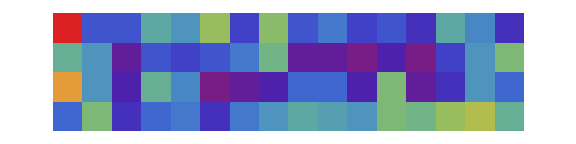

```mathematica
graph = ArrayPlot[stddev,PlotTheme->"Scientific",ImageSize->Large,AspectRatio->4/16,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

```mathematica
Export["/Users/atyndall/Dropbox/ash-honours/thesis/diagrams/stddev-contour2.pdf", graph]
```

/Users/atyndall/Dropbox/ash-honours/thesis/diagrams/stddev-contour2.pdf